```mathematica
runs={}
popsize=10000;
mutrate1={.000000390625,.000001562,.00000625,.000025,.0001,.0004,0.0016,0.0064};
mutrate2={.0000000390625,.0000001562,.000000625,.0000025,.00001,.00004,0.00016,0.00064};
generations=1000000;
DFE1=ExponentialDistribution[1/.01];
DFE2=ExponentialDistribution[1/.01];
cycles = 1000;
```

```mathematica
Do[
count1=0;
count2=0;
meanGen=0;
Do[
pop=Table[{0.,{},{}},{popsize}];
k=0;
Do[
Do[(*mutation*)
If[RandomReal[]<mutrate1[[j]],
mut=RandomVariate[DFE1];
If[pop[[i,1]]==0,
pop[[i,1]]+=mut;
AppendTo[pop[[i,2]],mut]
]];
If[RandomReal[]<mutrate2[[j]],
mut=RandomVariate[DFE2];
If[pop[[i,1]]==0,
pop[[i,1]]+=mut;
AppendTo[pop[[i,3]],mut]
]],
{i,Length[pop]}];
(*sampling*)
pop=RandomChoice[E^pop[[All,1]]->pop,Length[pop]];
If[Length[Intersection@@pop[[All,2]]]+Length[Intersection@@pop[[All,3]]]>0,Break[]];
k+=1,
{generations}];
meanGen+=k;
count1+=Length[Intersection@@pop[[All,2]]];
count2+=Length[Intersection@@pop[[All,3]]];,
(cycles)];
runs=AppendTo[runs,{popsize, mutrate1[[j]],mutrate2[[j]],generations,count1,count2,N[meanGen/cycles]}];
,{j,Length[mutrate1]}];
```

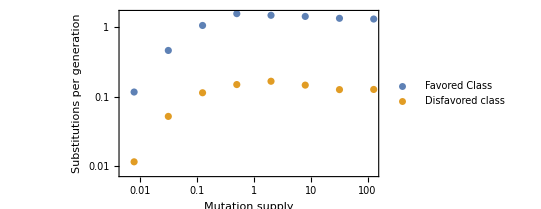

```mathematica
Show[ListLogLogPlot[
{2Table[{runs[[i,1]]runs[[i,2]],runs[[i,5]]/runs[[i,7]]*cycles},{i, Length[runs]}],
2 Table[{runs[[i,1]]runs[[i,2]],runs[[i,6]]/runs[[i,7]]*cycles},{i, Length[runs]}]},PlotLabels->Automatic,AspectRatio->Automatic,Frame->True, FrameLabel->{"Mutation supply","Substitutions per generation"},PlotLegends->{"Favored Class","Disfavored class"}]
]
```

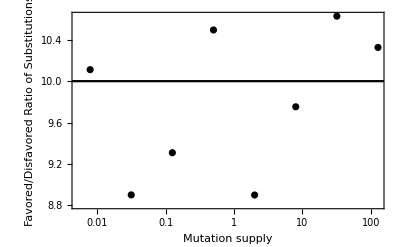

```mathematica
Show[ListLogLinearPlot[
Table[{2runs[[i,1]]runs[[i,2]],runs[[i,5]]/runs[[i,6]]},{i, Length[runs]}],Frame->True, FrameLabel->{"Mutation supply","Favored/Disfavored Ratio of Substitutions"},PlotStyle->Black],
LogLinearPlot[10,{x,.00001,1000},PlotStyle->Black]
]
```